```mathematica
STINRsnoise=ParallelTable[
pts=RandomPointConfiguration[PoissonPointProcess[100,2],Disk[]];
norms={};
Do[norms={norms,Norm[pts[[1]][[1]][[iii]]]},{iii,1,Length[pts[[1]][[1]]]}];
norms=Flatten[norms];
norms=Sort[norms];
stinr=1./(10.*norms[[1]])^4./(Total[1/(10*norms)^4.]+100.),100000
];
```

```mathematica
STINRsnoise=STINRsnonoise;
```

```mathematica
STINRsnoise=ParallelTable[STINR[simulatearealization[r,h,lambdaUE,0][[4]],1],100000];
```

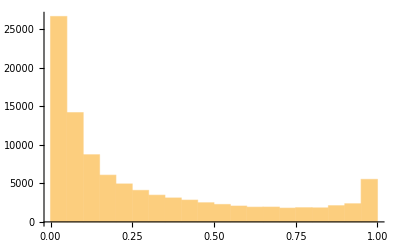

```mathematica
Histogram[STINRsnoise]
```

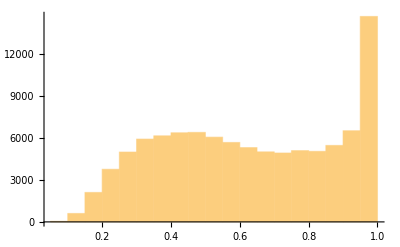

```mathematica
Histogram[STINRsnonoise]
```

```mathematica
.b4
```

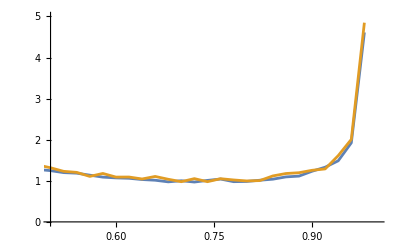

```mathematica
δ=0.02;
hist1=HistogramList[STINRsnonoise,{δ},"PDF"];
ys1=hist1[[2]];
xs1=Table[x,{x,Min[hist1[[1]]],Max[hist1[[1]]]-δ,δ}];hist2=HistogramList[STINRsnoise,{δ},"PDF"];
ys2=hist2[[2]];
xs2=Table[x,{x,Min[hist2[[1]]],Max[hist2[[1]]]-δ,δ}];
ListLinePlot[{Transpose[{xs1,ys1}],Transpose[{xs2,2.8*ys2}]},PlotRange->{{0.5,1},{0,5}}]
```